Особые точки

{{0,0},{1,-1},{2,0}}

Собственные значения линеаризации

{{-2,2},{-ⅈ √2,ⅈ √2},{-2,2}}

Седло, {0,0}

v1: {{-1,4}} v2: {{1,0}}

Центр, {1,-1}

Седло, {2,0}

v1: {{1,0}} v2: {{1,4}}

{Null,Null,Null,Null}

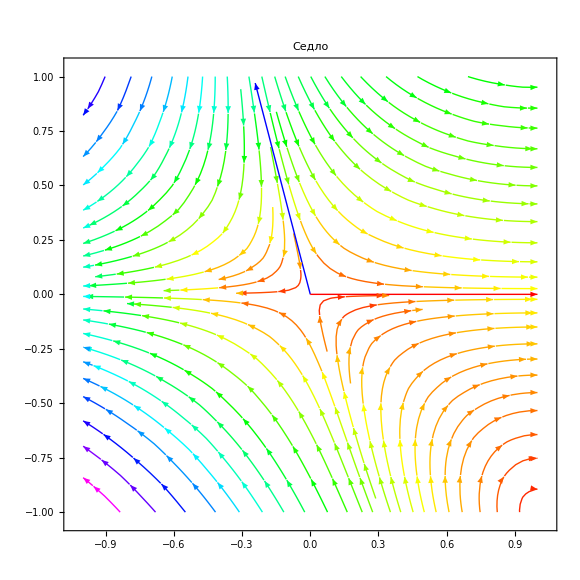
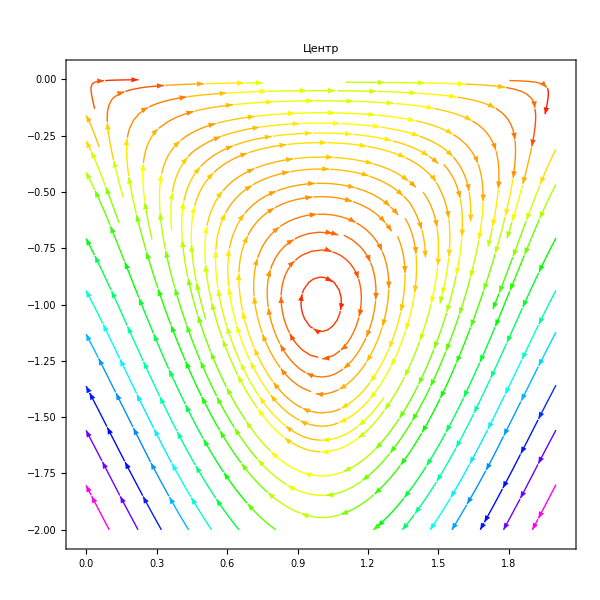
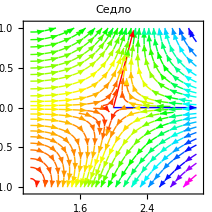

```mathematica
(*
Данная программа исследует дифференциальные уравнения на устойчивость в особых точках. Также классифицирует их. 
Обращаю внимание, что на графиках при выводе красный вектор - касается векторное поле, а синий вектор - второй собственный вектор линеаризованной системы. 
*)
P[x_, y_] :=y - x^2+2x
Q[x_, y_] := 2y*(x-1)
(* #4 
P[x_, y_] := x^2-y
Q[x_, y_] := (x-y)*(x-y+2) *)
(* #11 
P[x_, y_] := Sqrt[x^2-y+2]-2
Q[x_, y_] := ArcTan[x^2+x*y] *)
(* #14
P[x_, y_] := 2x+y^2-1
Q[x_, y_] := 6x-y^2+1 *)
(* #19 
P[x_, y_] := 1-x^2-y^2
Q[x_, y_] := 2x *)
(* #28
P[x_, y_] := x*y-4y-3x^2+12x
Q[x_, y_] := x^2-1 *)
q = Solve[P[x,y] == k * Q[x, y], k, Reals];
q = k/.q;
(*Если одно уравнение есть линейной комбинацией другой системы, то искусственно это проверяю, потому что вольфрам не умеет решать такие уравнения, по крайней для меня в удобном виде *)
If[NumberQ[q[[1]]], { Print["Пучок прямых"], StreamPlot[{P[x,y], Q[x,y]}, {x, -1, 1}, {y, -1, 1}, StreamColorFunction->Hue, PlotLabel->"Пучок прямых"]},{
(*Нахожу множество особых точек*)
Points = Solve[{P[x, y] == 0, Q[x,y] == 0}, {x,y}, Reals];
Points = {x,y}/.Points;
A = {};
(*Произвожу линеаризацию системы*)
For[i = 1, i <= Length[Points], i++, { Plx[x_, y_] = D[P[x,y], x], Ply[x_, y_] = D[P[x,y], y],Qlx[x_, y_] = D[Q[x,y], x],Qly[x_, y_] = D[Q[x,y], y], AppendTo[A,{{Plx[Points[[i, 1]], Points[[i, 2]]], Ply[Points[[i, 1]], Points[[i, 2]]]}, {Qlx[Points[[i, 1]], Points[[i, 2]]], Qly[Points[[i, 1]], Points[[i, 2]]]}}]}],
(*Нахожу множество собственных значений линеаризованной системы*)
lam = {};
For[i = 1, i ≤Length[Points], i++, {AppendTo[lam, Solve[Det[A[[i]] - x*{{1, 0}, {0,1}}] == 0, x]]}],
lam = x/.lam;
(*Сортирую каждую пару собственных значений, чтобы знать какой собственный вектор будет касаться векторное поле*)
For[i = 1, i < Length[lam], i++, Sort[lam[[i]]]],
Print["Особые точки"];
Print[Points];
Print["Собственные значения линеаризации"];
Print[lam];
Gr = {};
For[i = 1, i ≤ Length[Points], i++, { 
(*Разбиваю всю систему на два случая: когда собственные числа действительные или мнимые*)
If[Im[lam[[i,1]]] == 0, {
If[lam[[i,1]] * lam[[i,2]] == 0 ,  { Print["Пучок прямых, ", Points[[i]]], AppendTo[Gr, StreamPlot[{P[x,y], Q[x,y]}, {x, Points[[i,1]]-1, Points[[i,1]]+1}, {y, Points[[i,2]]-1, Points[[i,2]]+1}, StreamColorFunction->Hue, PlotLabel->"Пучок прямых"]];},
{ 
If[lam[[i,1]] ==  lam[[i,2]], {
u = NullSpace[A[[i]] - lam[[i,1]] * {{1,0}, {0,1}}];
If[Length[u] == 2,  { Print["Дикритический узел, ", Points[[i]]], AppendTo[Gr, StreamPlot[{P[x,y], Q[x,y]}, {x, Points[[i,1]]-1, Points[[i,1]]+1}, {y, Points[[i,2]]-1, Points[[i,2]]+1}, StreamColorFunction->Hue, PlotLabel->"Дикритический узел"]];} ,
{ Print["Вырожденный узел, ", Points[[i]]], Print["v: ", u], AppendTo[Gr, StreamPlot[{P[x,y], Q[x,y]}, {x, Points[[i,1]]-1, Points[[i,1]]+1}, {y, Points[[i,2]]-1, Points[[i,2]]+1}, StreamColorFunction->Hue, PlotLabel->"Вырожденный узел", Epilog->{{Red, Arrow[{{Points[[i,1]], Points[[i,2]]}, {Points[[i,1]] + u[[1,1]]/Sqrt[(u[[1,1]]^2+u[[1,2]]^2)], Points[[i,2]] + u[[1,2]]/Sqrt[(u[[1,1]]^2+u[[1,2]]^2)]}}]}}]];
}]
},
{
If[lam[[i,1]] < 0 && lam[[i,2]] < 0, { Print["Устойчивый узел, ", Points[[i]]], u = NullSpace[A[[i]] - lam[[i,1]] * {{1,0}, {0,1}}], v = NullSpace[A[[i]] - lam[[i,2]] * {{1,0}, {0,1}}], Print["v1: ", u, " v2: ", v],  AppendTo[Gr, StreamPlot[{P[x,y], Q[x,y]}, {x, Points[[i,1]]-1, Points[[i,1]]+1}, {y, Points[[i,2]]-1, Points[[i,2]]+1}, StreamColorFunction->Hue, PlotLabel->"Устойчивый узел", Epilog->{{Blue, Arrow[{{Points[[i,1]], Points[[i,2]]}, {Points[[i,1]] + u[[1,1]]/Sqrt[(u[[1,1]]^2+u[[1,2]]^2)], Points[[i,2]] + u[[1,2]]/Sqrt[(u[[1,1]]^2+u[[1,2]]^2)]}}]}, {Red, Arrow[{{Points[[i,1]], Points[[i,2]]}, {Points[[i,1]] + v[[1,1]]/Sqrt[(v[[1,1]]^2+v[[1,2]]^2)], Points[[i,2]] + v[[1,2]]/Sqrt[(v[[1,1]]^2+v[[1,2]]^2)]}}]}}]];}],
If[lam[[i,1]] > 0 && lam[[i,2]] > 0, { Print["Неустойчивый узел, ", Points[[i]]], u = NullSpace[A[[i]] - lam[[i,1]] * {{1,0}, {0,1}}], v = NullSpace[A[[i]] - lam[[i,2]] * {{1,0}, {0,1}}], Print["v1: ", u, " v2: ", v],  AppendTo[Gr, StreamPlot[{P[x,y], Q[x,y]}, {x, Points[[i,1]]-1, Points[[i,1]]+1}, {y, Points[[i,2]]-1, Points[[i,2]]+1}, StreamColorFunction->Hue, PlotLabel->"Неустойчивый узел", Epilog->{{Red,Arrow[{{Points[[i,1]], Points[[i,2]]}, {Points[[i,1]] + u[[1,1]]/Sqrt[(u[[1,1]]^2+u[[1,2]]^2)], Points[[i,2]] + u[[1,2]]/Sqrt[(u[[1,1]]^2+u[[1,2]]^2)]}}]}, {Blue, Arrow[{{Points[[i,1]], Points[[i,2]]}, {Points[[i,1]] + v[[1,1]]/Sqrt[(v[[1,1]]^2+v[[1,2]]^2)], Points[[i,2]] + v[[1,2]]/Sqrt[(v[[1,1]]^2+v[[1,2]]^2)]}}]}}]];}],
If[lam[[i,1]] *lam[[i,2]] < 0, { Print["Седло, ", Points[[i]]], u = NullSpace[A[[i]] - lam[[i,1]] * {{1,0}, {0,1}}], v = NullSpace[A[[i]] - lam[[i,2]] * {{1,0}, {0,1}}], Print["v1: ", u, " v2: ", v],  AppendTo[Gr, Show[{StreamPlot[{P[x,y], Q[x,y]}, {x, Points[[i,1]]-1, Points[[i,1]]+1}, {y, Points[[i,2]]-1, Points[[i,2]]+1}, StreamColorFunction->Hue, PlotLabel->"Седло", Epilog->{{Blue,Arrow[{{Points[[i,1]], Points[[i,2]]}, {Points[[i,1]] + u[[1,1]]/Sqrt[(u[[1,1]]^2+u[[1,2]]^2)], Points[[i,2]] + u[[1,2]]/Sqrt[(u[[1,1]]^2+u[[1,2]]^2)]}}]}, {Red, Arrow[{{Points[[i,1]], Points[[i,2]]}, {Points[[i,1]] + v[[1,1]]/Sqrt[(v[[1,1]]^2+v[[1,2]]^2)], Points[[i,2]] + v[[1,2]]/Sqrt[(v[[1,1]]^2+v[[1,2]]^2)]}}]}}]}]];}]
}]}]
}, 
{
If[Re[lam[[i,1]]] > 0, { Print["Неустойчивый фокус, ", Points[[i]]],AppendTo[Gr, StreamPlot[{P[x,y], Q[x,y]}, {x, Points[[i,1]]-1, Points[[i,1]]+1}, {y, Points[[i,2]]-1, Points[[i,2]]+1}, StreamColorFunction->Hue, PlotLabel->"Неустойчивый фокус"]]}],
If[Re[lam[[i,1]]] == 0, { Print["Центр, ", Points[[i]]],AppendTo[Gr, StreamPlot[{P[x,y], Q[x,y]}, {x, Points[[i,1]]-1, Points[[i,1]]+1}, {y, Points[[i,2]]-1, Points[[i,2]]+1}, StreamColorFunction->Hue, PlotLabel->"Центр"]]}],
If[Re[lam[[i,1]]] < 0, { Print["Устойчивый фокус, ", Points[[i]]],AppendTo[Gr, StreamPlot[{P[x,y], Q[x,y]}, {x, Points[[i,1]]-1, Points[[i,1]]+1}, {y, Points[[i,2]]-1, Points[[i,2]]+1}, StreamColorFunction->Hue, PlotLabel->"Устойчивый фокус"]]}]
}]
}]}]
Gr
```